```mathematica
<<TopoTB`
```

#### Band

```mathematica
?VASPBand
```

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
eigenval=Import["EIGENVAL","Table"];
efermi=-2.0707;
```

```mathematica
(*ISPIN=2,SOC=1*)
ds=VASPBand[poscar,kpoints,eigenval,efermi,2,1,"Band.dat"]
```

Dataset[<>]

```mathematica
?BandLabelsPlot
```

```mathematica
KK=Normal[ds[5]];
KK=KK/.{KK[[4,2]]->"-K"}
tband=Normal[ds[7]];
```

{{0.,Γ},{1.1169,K},{1.67535,M},{2.2338,-K},{3.35071,Γ}}

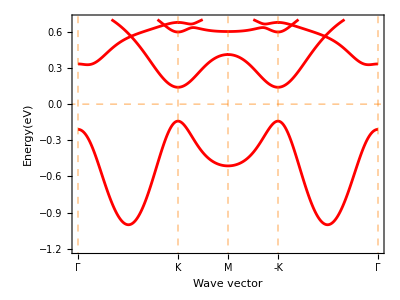

```mathematica
(*spin up*)
tbandup=Table[tband[[i]][[All,{1,2}]],{i,1,Length[tband]}];
figup=BandPlot[tbandup,KK,Red,0.005,3/4,{-1.2,0.7}]
```

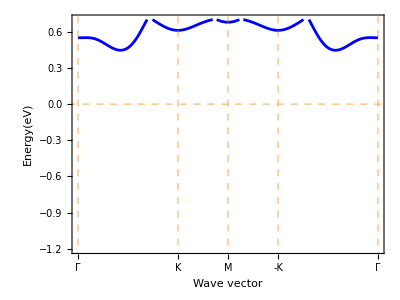

```mathematica
(*spin down*)
tbanddown=Table[tband[[i]][[All,{1,3}]],{i,1,Length[tband]}];
figdown=BandPlot[tbanddown,KK,Blue,0.005,3/4,{-1.2,0.7}]
```

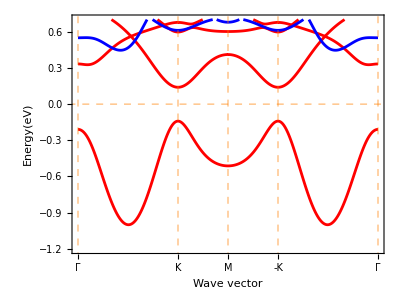

```mathematica
Show[figup,figdown]
```

```mathematica
tbandup=Table[tband[[i]][[All,{1,2}]],{i,1,Length[tband]}];
BandLabelsPlot[tbandup,KK,Red,0.005,3/4,{-1.2,0.7}]
```

-Graphics-

#### PBand

```mathematica
?VASPPBand
```

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
procar=Import["PROCAR","Table"];
efermi=-2.0707;
```

```mathematica
(*ISPIN=2,UpOrDown=1(spin up),SOC=1*)
ds1=VASPPBand[poscar,kpoints,procar,efermi,2,1,1,{0},"PBand-up.dat"]
```

Dataset[<>]

```mathematica
(*ISPIN=2,UpOrDown=1(spin down),SOC=1*)
ds2=VASPPBand[poscar,kpoints,procar,efermi,2,2,1,{0},"PBand-down.dat"]
```

Dataset[<>]

```mathematica
?PBandPlot
```

```mathematica
(*spin up*)
KK1=Normal[ds1[5]];
KK1=KK1/.{KK1[[4,2]]->"-K"}
tpband1=Normal[ds1[7]];
Normal[ds1[6]]
```

{{0.,Γ},{1.1169,K},{1.67535,M},{2.2338,-K},{3.35071,Γ}}

<|K-Path(1/Å)→{1},Energy(eV)→{2},s→{3},py→{4},pz→{5},px→{6},dxy→{7},dyz→{8},dz2→{9},dxz→{10},x2-y2→{11},fy3x2→{12},fxyz→{13},fyz2→{14},fz3→{15},fxz2→{16},fzx2→{17},fx3→{18},tot→{19}|>

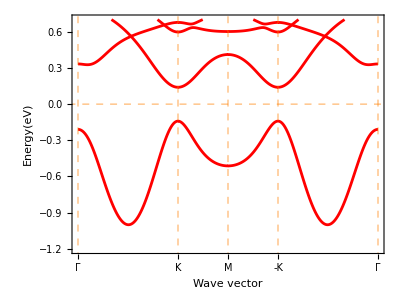

```mathematica
tpbandup=Table[tpband1[[i]][[All,{1,2}]],{i,1,Length[tpband1]}];
figup=BandPlot[tpbandup,KK1,Red,0.005,3/4,{-1.2,0.7}]
```

```mathematica
(*spin down*)
KK2=Normal[ds2[5]];
KK2=KK2/.{KK2[[4,2]]->"-K"}
tpband2=Normal[ds2[7]];
Normal[ds2[6]]
```

{{0.,Γ},{1.1169,K},{1.67535,M},{2.2338,-K},{3.35071,Γ}}

<|K-Path(1/Å)→{1},Energy(eV)→{2},s→{3},py→{4},pz→{5},px→{6},dxy→{7},dyz→{8},dz2→{9},dxz→{10},x2-y2→{11},fy3x2→{12},fxyz→{13},fyz2→{14},fz3→{15},fxz2→{16},fzx2→{17},fx3→{18},tot→{19}|>

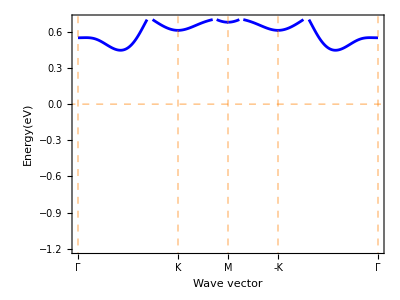

```mathematica
tpbanddown=Table[tpband2[[i]][[All,{1,2}]],{i,1,Length[tpband1]}];
figdown=BandPlot[tpbanddown,KK2,Blue,0.005,3/4,{-1.2,0.7}]
```

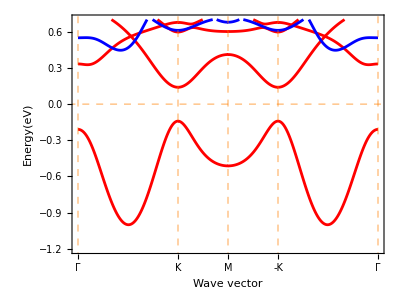

```mathematica
Show[figup,figdown]
```